# Spintore CMV

## 1. As-it-is Kinematics

-Graphics--Graphics-

The geometrical data are

```mathematica
(*sides [mm]*)
L1 =2133 ;
L2 = 1100;
L3 = 1400;
L4 = 1000;
```

```mathematica
(*actuator initial length[mm]*)
s0=1412;
```

Define the initial configuration

We are interested in defining the angles of the segments OB and CD in order to describe consequently the transmitted forces since these elements can be loaded only in traction or compression.
Consequently we are interested in obtaining the absolute position of the point to describe the potion of the mechanism.

```mathematica
(*constant positions (grounded)[mm]*)
xO = 0;
yO = 0;
xA = 2365;
yA =1900;
```

In order  to find θ1, θ2 and  θ3 we apply trigonometry referring to the image above.

```mathematica
solth1th2=(Simplify@Solve[{
xA ==s*Cos[θ1]+L1*Sin[Pi/2-θ2],
yA == -s*Sin[θ1]+L1*Cos[Pi/2-θ2]
},{θ1,θ2}]/.C[1]->0/.C[2]->0)[[2]];
```

```mathematica
solth3 = (Simplify@Solve[L3*Sin[Pi/2-θ3]==L2(Cos[Pi/2-θ2]-1)/.solth1th2,{θ3}]/.C[1]->0)[[2]][[1]];
```

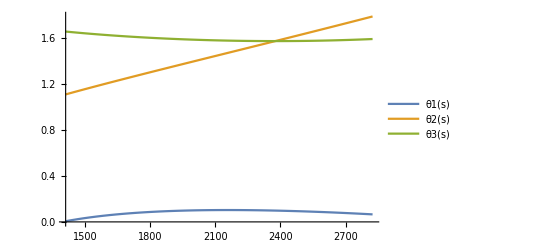

```mathematica
Plot[{θ1/.solth1th2,θ2/.solth1th2,θ3/.solth3},{s,s0,2*s0},PlotLegends->{"θ1(s)","θ2(s)","θ3(s)"}]
```

The values of θ1, θ2, θ3 in the initial configuration are:

```mathematica
(*[rad]*)
θ10 = N[θ1/.solth1th2/.s->s0]
```

0.00584577

```mathematica
θ20 = N[θ2/.solth1th2/.s->s0]
```

1.10761

```mathematica
θ30 = N[θ3/.solth3/.s->s0]
```

1.65368

Now that we have defined the 3 angular coordinates, we can define all the points on the mechanism.

```mathematica
xB = Simplify[s*Cos[θ1]/.solth1th2];
yB = Simplify[-s*Sin[θ1]/.solth1th2];
```

```mathematica
xC = Simplify[xA+ L2*Cos[Pi/2-θ2]/.solth1th2];
yC =Simplify[ yA-L2*Sin[Pi/2-θ2]/.solth1th2];
```

```mathematica
xD =Simplify[ xC/.s->s0];
```

```mathematica
yD = Simplify[yC + L3 * Cos[θ3-Pi/2]/.solth3];
```

In order to find the upper boundary for s, we compute the maximum permissible yD given by CMV.
The total race of point D is 975 mm

```mathematica
s0
```

1412

```mathematica
yD0 = N[yD/.s->s0]
```

2803.71

```mathematica
NSolve[yD == 975+yD0,s][[2]][[1]]
```

s→3301.98

```mathematica
smax = 3302;
```

The animation of the motion can be visualized below.

```mathematica
Manipulate[
Show[
ListPlot[{{xO,yO},{xB,yB}}/.s->S,Joined->True,PlotRange->{{-500,4000},{-500,4000}},AspectRatio->1,PlotStyle->Blue,PlotMarkers->"O"],
Graphics[{Pink,Triangle[{{xA,yA},{xB,yB},{xC,yC}}/.s->S],Gray,Line[{{xD,-500},{xD,4000}}]}],
ListPlot[{{xC,yC},{xD,yD}}/.s->S,Joined->True,PlotStyle->Red,PlotMarkers->"O"],
Graphics[{PointSize[Large],Point[{{xO,yO},{xA,yA}}]}]
],
{S,s0,smax}]
```

```mathematica
θ1max = N[θ1/.solth1th2/.s->smax]
```

0.00490392

```mathematica
θ2max = N[θ2/.solth1th2/.s->smax]
```

2.02558

```mathematica
Pi-θ2max(*[rad]*)
```

1.11601

```mathematica
θ3max = N[θ3/.solth3/.s->smax]
```

1.65074

## 2. As-it-is Reaction forces

## PUSHER

-Graphics-

Since the total mass is 423000 [kg], and the friction coefficient is SUPPOSED to be 0.8,
the total load to move is 3.32*10^6 [N].
Each force F is assumed to be equal and therefore

```mathematica
F = 332000; (*[N]*)
```

Considering the center of moments as shown in the picture, all the moments produced by F cancel out.
Only the forces produced by the rods have a contribution.
Using the momentum and translation equilibrium:

```mathematica
b =4125; (*[mm]*)
```

```mathematica
NSolve[{Fr1y*b==Fr2y*b,Fr1y+Fr2y==10*F},{Fr1y,Fr2y}]
```

{{Fr1y→1.66×10^6,Fr2y→1.66×10^6}}

Of course both the 2 forces Fr1y and Fr2y are equal and are:

```mathematica
Fry = 1.66*10^6; (*[N]*)
```

The forces Frx1 = Frx2 = Frx are to be found starting from the lever mechanism (cannot be solved by equilibrium in this subsystem).

The longitudinal force acting on the rod is :

```mathematica
Frx = Fry*1/Tan[Pi-θ3]/.solth3;
```

```mathematica
Fr = √(Frx^2+Fry^2);
```

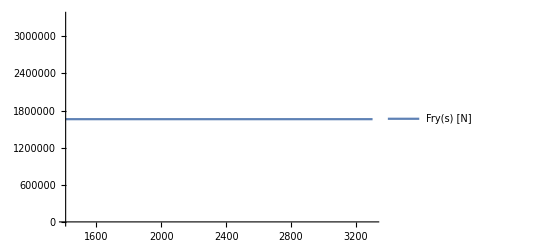
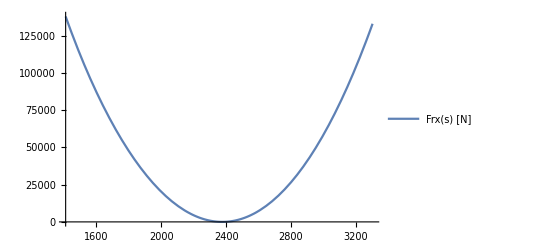
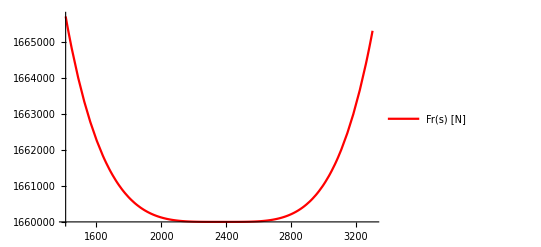

```mathematica
{Plot[{Fry},{s,s0,smax},PlotLegends->{"Fry(s) [N]"}],
Plot[{Frx},{s,s0,smax},PlotLegends->{"Frx(s) [N]"}],
Plot[{Fr},{s,s0,smax},PlotLegends->{"Fr(s) [N]"},PlotStyle->Red]}
```

## LEVER

-Graphics--Graphics-

We apply the equilibrium of forces and torques with respect of A.

```mathematica
FCx = Frx
FCy = Fry
```

(0.000166105 (2626084250 s+380 s^3-473 √(-s^2 (21655397303296-27505828 s^2+s^4))))/(s √(1-(121 (2626084250 s+380 s^3-473 √(-s^2 (21655397303296-27505828 s^2+s^4)))^2)/(12084754840587896720400 s^2)))

1.66×10^6

```mathematica
FBx = FB*Cos[θ1]/.solth1th2;
FBy = FB*Sin[θ1]/.solth1th2;
```

```mathematica
solFex0=Simplify@Solve[{
(*eq x*)0==FCx+FAx+FBx-FEx/.solth1th2/.FEx->0,
(*eq y*)0==-FCy + FAy-FBy/.solth1th2/.FEx->0,
(*rq A*)0==-FCy*L2*Cos[Pi/2-θ2]+FCx*L2*Sin[Pi/2-θ2]-FEx*(L1-L4)*Cos[θ2]+FBx*L1*Sin[θ2]+FBy*L1*Cos[θ2]/.solth1th2/.FEx->0
}
,{FAx,FAy,FB}][[1]];
```

```mathematica
FA = √(FAx^2+FAy^2)/.solFex0;
```

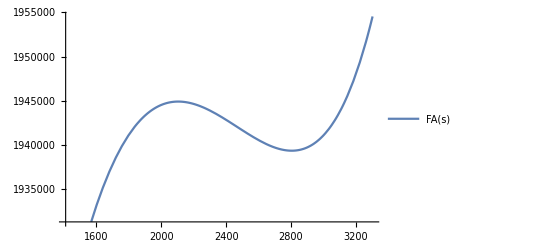
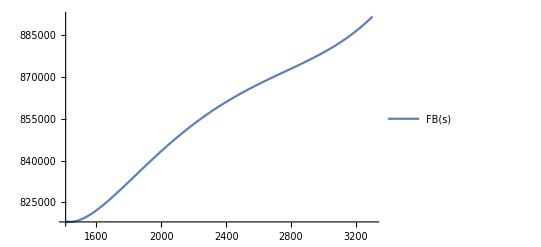

```mathematica
{Plot[{FA},{s,s0,smax},PlotLegends->{"FA(s)"}],Plot[{FB/.solFex0},{s,s0,smax},PlotLegends->{"FB(s)"}]}
```

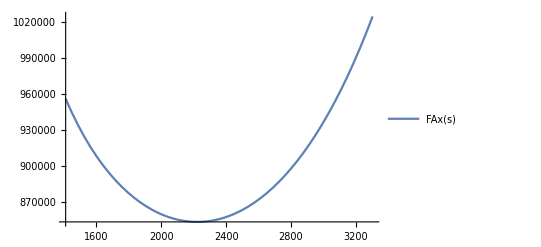
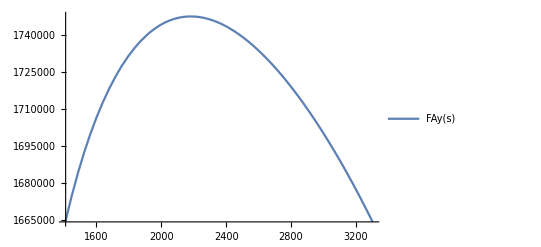

```mathematica
{Plot[{Abs[FAx]/.solFex0},{s,s0,smax},PlotLegends->{"FAx(s)"}],Plot[{FAy/.solFex0},{s,s0,smax},PlotLegends->{"FAy(s)"}]}
```

We find a local maximum of the function FA and then check the extremes for absolute maximums

```mathematica
Max[FindMaximum[FA,{s,s0}][[1]],FA/.s->s0,FA/.s->smax]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.95454×10^6

Which corresponds to s →s_max
The race of the jack is:

```mathematica
smax-s0
```

1890

The force required from the actuator is:

```mathematica
Max[
FindMaximum[FB/.solFex0,{s,s0}][[1]],
FB/.solFex0/.s->s0,
FB/.solFex0/.s->smax
]
```

FindMaximum::nrnum: The function value -299557.+392129. ⅈ is not a real number at {s} = {706.}.

891758.

## 3. As-it-is Middle bar influence

It might happen that the pressure in the actuators is not perfectly equal (within tolerances), in this case the middle bar is designed in order to redistribute the force on both levers. 
How is it loaded?
NB: we are interested in the maximum load when the actuator reaches it’s maximum elongation at s -> smax.

Let’s say that the actuator 1 is working correctly and applying a force FB (stated before), while the actuator 2 is applying only αFB where 0< α  <1.
From the momentum equilibrium we can evaluate FE.

## MECHANISM 2

-Graphics-

NOTE THAT THIS IS AN EVALUATION REGARDING THE SECOND LEVER, THE FIRST ONE WILL NEED ANOTHER EVALUATION ON IT’S OWN

```mathematica
(*Force applied by second actuator [N]*)
FB2 = α*FB/.solFex0/.s->smax
```

891758. α

```mathematica
(*x and y components [N]*)
FBx2 = α*FB*Cos[θ1]/.solth1th2/.solFex0/.s->smax
FBy2 = α*FB*Sin[θ1]/.solth1th2/.solFex0/.s->smax
```

891747. α

4373.09 α

```mathematica
(*resisting load at point C [N]*)
FCx2=FCx/.s->smax
FCy2=FCy/.s->smax
```

132998.

1.66×10^6

```mathematica
(*Equilibrium of forces and torques with contribution of bar*)
sol2max =Solve[{
(*eq x*)0==FCx2-FAx2+FBx2+FEx2,
(*eq y*)0==FCy2 - FAy2+FBy2,
(*eq A*)0==-FCy2*L2*Cos[θ2-Pi/2]-FCx2*L2*Sin[θ2-Pi/2]+FEx2*(L1-L4)*Cos[θ2-Pi/2]+FBx2*L1*Cos[θ2-Pi/2]-FBy2*L1*Sin[θ2-Pi/2]/.solth1th2/.s->smax
}
,{FAx2,FAy2,FEx2}][[1]]
```

{FAx2→1.80779×10^6-783041. α,FAy2→1.66×10^6+4373.09 α,FEx2→1.67479×10^6-1.67479×10^6 α}

```mathematica
(*resulting force on pin [N]*)
FAmax2 = √(FAx2^2+FAy2^2)/.sol2max
```

√((1.80779×10^6-783041. α)^2+(1.66×10^6+4373.09 α)^2)

```mathematica
(*resulting force on bar [N]*)
FEmax = FEx2/.sol2max
```

1.67479×10^6-1.67479×10^6 α

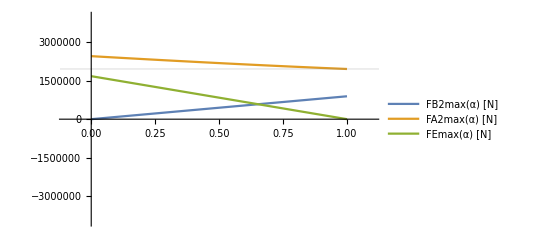

```mathematica
Plot[{FB2,FAmax2,FEmax},
{α,0,1},PlotRange->{{-0.1,1.1},{-4*10^6,4*10^6}},PlotLegends->{"FB2max(α) [N]","FA2max(α) [N]","FEmax(α)  [N]"}
,GridLines->{None,{FA/.s->smax}}]
```

The middle bar will need to withstand an axial load (assuming α = 0 as complete failure of one of the 2 jacks) of :

```mathematica
FbarMAX=(FEx2/.sol2max/.α->0)(* [N] *)
```

1.67479×10^6

The pin will need to withstand an axial load (assuming α = 0 as complete failure of one of the 2 jacks) of :

```mathematica
Fpin2MAX=(FAmax2/.sol2max/.α->0)(* [N] *)
```

2.45432×10^6

## MECHANSIM 1

-Graphics-

The new equilibrium is defined with the contribution of FE, still evaluated at s-> smax.
Given the resisting forces and the bar force, which are the actuator and pin forces at lever 1?

```mathematica
(*components of actuator 1 force*)
FBx1 =N@Simplify[FB1*Cos[θ1]/.solth1th2/.s->smax]
FBy1 =N@Simplify[FB1*Sin[θ1]/.solth1th2/.s->smax]
```

0.999988 FB1

0.0049039 FB1

```mathematica
(*resisting forces at C [N]*)
FCx1 = FCx/.s->smax
FCy1 = FCy/.s->smax
```

132998.

1.66×10^6

```mathematica
(*bar force [N]*)
FEx1 = FEx2/.sol2max
```

1.67479×10^6-1.67479×10^6 α

```mathematica
(*new equilibrium of forces and torques*)
sol1max =Solve[{
(*eq x*)0==FCx1+FAx1+FBx1-FEx1,
(*eq y*)0==FCy1 - FAy1+FBy1,
(*eq A*)0==-FCy1*L2*Cos[θ2-Pi/2]-FCx1*L2*Sin[θ2-Pi/2]-FEx1*(L1-L4)*Cos[θ2-Pi/2]+FBx1*L1*Cos[θ2-Pi/2]-FBy1*L1*Sin[θ2-Pi/2]/.solth1th2/.s->smax
}
,{FAx1,FAy1,FB1}][[1]]
```

{FAx1→-241704.-783041. α,FAy1→1.66875×10^6-4373.09 α,FB1→1.78352×10^6-891758. α}

```mathematica
(*force acting on pin [N]*)
FAmax1=√(FAx1^2+FAy1^2) /.sol1max
```

√((-241704.-783041. α)^2+(1.66875×10^6-4373.09 α)^2)

```mathematica
FB1max=FB1/.sol1max;
```

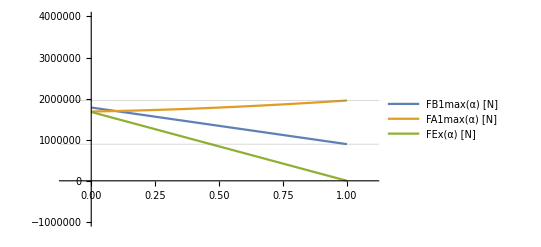

```mathematica
Plot[{FB1max,FAmax1,FEx1},
{α,0,1},PlotRange->{{-0.1,1.1},{-10^6,4*10^6}},PlotLegends->{"FB1max(α) [N]","FA1max(α) [N]","FEx(α) [N]"},
GridLines->{None,{FA/.s->smax,FB/.solFex0/.s->smax}}]
```

The actuator will need to withstand an axial load (assuming α = 0 as complete failure of one of the 2 jacks) of :

```mathematica
FB1MAX=(FB1max/.α->0)(* [N] *)
```

1.78352×10^6

The pin will need to withstand an axial load (assuming α = 0 as complete failure of one of the 2 jacks) of :

```mathematica
Fpin1MAX=(FAmax1/.sol2max/.α->0)(* [N] *)
```

1.68616×10^6

## WITH GIVEN ACTUATOR PRESSURE

-Graphics-

The aim is to evaluate the dynamic evolution of the system given the working regimes of the two actuators.
The two pressure in the piston cylinders in two different cases are:
-  p1 = 140 [bar], p2 = 0.9*140[bar]				---> already considered critical
- p1 = 140 [bar] , p2 = 0 [bar] 					---> complete failure of one of the two actuators

For both pistons the pressure acts on an area  = π/4(.280)^2=61575 [mm^2] 

Then the force in [N] produced in the two cases is f = p*area:
- fB1 = 140/10*61575 [bar/10*mm^2] = [MPa * mm^2] = 862’050[N] 		and 		fB2 = 775’845 [N]
- fB1 = 862’050[N]										and 		fB2 = 0 [N]

In this case the force of the actuators has an upper boundary, therefore we must evaluate the maximum resisting load at point C (pusher rod) that can  be sustained.

### p1 = 140 [bar] , p2 = 0.9*140 [bar]

```mathematica
(*actuators axial force [N]*)
fB1 = 862050;
fB2 = 775845;
```

```mathematica
(*x and y components [N]*)
fBx1 = N@fB1*Cos[θ1]/.solth1th2/.s->smax
fBy1 =N@ fB1*Sin[θ1]/.solth1th2/.s->smax
fBx2 = N@fB2*Cos[θ1]/.solth1th2/.s->smax
fBy2 =N@ fB2*Sin[θ1]/.solth1th2/.s->smax
```

862040.

4227.41

775836.

3804.67

```mathematica
(*relationship between fCx and fCy*)
fCx = Simplify[fCy*1/Tan[Pi-θ3]/.solth3/.s->smax]
```

-(121 (-61539107+688 √6225249965) fCy)/(√(22258767220137589035+1239767834247712 √6225249965))

```mathematica
(*solution to Newton-Euler equations for both mechanisms*)
s09 =Solve[{
(*++++++++++++++++++LEVER 1+++++++++++++++++++++*)
(*eq x*)0==fCx-fAx1+fBx1-fEx,
(*eq y*)0==fCy - fAy1+fBy1,
(*eq A*)0==-fCy*L2*Cos[θ2-Pi/2]-fCx*L2*Sin[θ2-Pi/2]-fEx*(L1-L4)*Cos[θ2-Pi/2]+fBx1*L1*Cos[θ2-Pi/2]-fBy1*L1*Sin[θ2-Pi/2]/.solth1th2/.s->smax,
(*++++++++++++++++++LEVER 2+++++++++++++++++++++*)
(*eq x*)0==fCx-fAx2+fBx2+fEx,
(*eq y*)0==fCy - fAy2+fBy2,
(*eq A*)0==-fCy*L2*Cos[θ2-Pi/2]-fCx*L2*Sin[θ2-Pi/2]+fEx*(L1-L4)*Cos[θ2-Pi/2]+fBx2*L1*Cos[θ2-Pi/2]-fBy2*L1*Sin[θ2-Pi/2]/.solth1th2/.s->smax
}
,{fAx1,fAy1,fAx2,fAy2,fEx,fCy}][[1]]
```

{fAx1→903229.,fAy1→1.52869×10^6,fAx2→978924.,fAy2→1.52827×10^6,fEx→80949.8,fCy→1.52446×10^6}

The axial force (which works in compression while pushing) on the bar is

```mathematica
fbar09 = fEx/.s09(*[N]*)
```

80949.8

The maximum resisting load that can be pushed (assuming no inertial contribution) is:

```mathematica
fC09 = √(fCy^2+fCx^2/.s09)(*[N]*)
```

1.52935×10^6

### p1 = 140 [bar] , p2 = 0 [bar]

In this case we propose the same analysis with fB2x and fB2y = 0

```mathematica
(*solution to Newton-Euler equations for both mechanisms*)
s00 =Solve[{
(*++++++++++++++++++LEVER 1+++++++++++++++++++++*)
(*eq x*)0==fCx-fAx1+fBx1-fEx,
(*eq y*)0==fCy - fAy1+fBy1,
(*eq A*)0==-fCy*L2*Cos[θ2-Pi/2]-fCx*L2*Sin[θ2-Pi/2]-fEx*(L1-L4)*Cos[θ2-Pi/2]+fBx1*L1*Cos[θ2-Pi/2]-fBy1*L1*Sin[θ2-Pi/2]/.solth1th2/.s->smax,
(*++++++++++++++++++LEVER 2+++++++++++++++++++++*)
(*eq x*)0==fCx-fAx2+fEx,
(*eq y*)0==fCy - fAy2,
(*eq A*)0==-fCy*L2*Cos[θ2-Pi/2]-fCx*L2*Sin[θ2-Pi/2]+fEx*(L1-L4)*Cos[θ2-Pi/2]/.solth1th2/.s->smax
}
,{fAx1,fAy1,fAx2,fAy2,fEx,fCy}][[1]]
```

{fAx1→116826.,fAy1→806577.,fAx2→873781.,fAy2→802350.,fEx→809498.,fCy→802350.}

The axial force (which works in compression while pushing) on the bar is

```mathematica
fbar00 = fEx/.s00(*[N]*)
```

809498.

The maximum resisting load that can be pushed (assuming no inertial contribution) is:

```mathematica
fC09 = √(fCy^2+fCx^2/.s00)(*[N]*)
```

804921.

## MIDDLE BAR STRESS ANALYSiS

### AS-IT-IS STATIC LOAD ANALYSIS

-Graphics-

Now that the maximum stress on the bar is known...

```mathematica
fbar00
fbar09
```

809498.

80949.8

... the minimum diameter of the component can be calculated using StVenant beam theory considering also the weight of the beam.

```mathematica
(*Bar length [mm]*)
```

```mathematica
Lbar = 8250;
```

Given the external and internal diameters dext, dint and the material 42CrMo4, the weight is:

```mathematica
(*as-it-is diameters [mm]*)
```

```mathematica
dext0 =273;
dint0 = 213; (*273-36*2 ma c'è anche una resitrizione di sezione*)
```

```mathematica
(*material density [kg/m^3]*)
ρ=7800;
```

```mathematica
(*cross section area [mm^2]*)
A = (π*(dext^2-dint^2))/4
```

1/4 (dext^2-dint^2) π

```mathematica
(*cross section inertia [mm^4]*)
Ix =Simplify[ (π*(dext^4-dint^4))/64]
```

1/64 (dext^4-dint^4) π

```mathematica
(*total weight [N], note that d and Lbar are expressed in [mm]*)
W =(A*Lbar)*10^-9*ρ*9.81
W0 = W/.dint->dint0/.dext->dext0
```

0.495801 (dext^2-dint^2)

14457.6

The maximum bending stress is obtained in the middle cross-section where

```mathematica
R=W/2
```

0.247901 (dext^2-dint^2)

```mathematica
Mx = R*Lbar/2(*Maximum bending torque, obtained in the middle of the bar[N*mm]*)
```

1022.59 (dext^2-dint^2)

```mathematica
Mx0 = Mx/.dint->dint0/.dext->dext0
```

2.98187×10^7

The axial stress evaluated at most critical point in middle cross-section is:

```mathematica
fbar00
```

809498.

```mathematica
(*SINGLE ACTUATOR CASE*)
σzz00 = FullSimplify[fbar00/A+Mx/Ix*dext/2](*Contribution of tensile and bending stresses[N/mm^2+(N*mm)/mm^4*mm]= [MPa]*)
```

(1.03068×10^6 dint^2+dext (dext (1.03068×10^6+10416. dext)-10416. dint^2))/(0.+dext^4-1. dint^4)

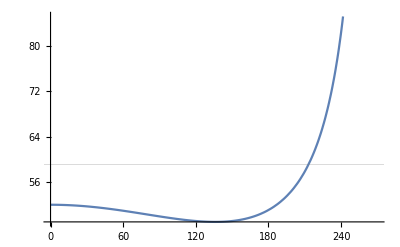

```mathematica
Plot[{σzz00/.dext->dext0},{dint,0,270},GridLines->{None,{σzz00/.dext->dext0/.dint->dint0}}]
```

```mathematica
(*PARTIALLY UNLOADED ACTUATOR CASE*)
σzz09 = FullSimplify[fbar09/A+Mx/Ix*dext/2](*Contribution of tensile and bending stresses[N/mm^2+(N*mm)/mm^4*mm]=[MPa]*)
```

(103068. dint^2+dext (dext (103068.+10416. dext)-10416. dint^2))/(0.+dext^4-1. dint^4)

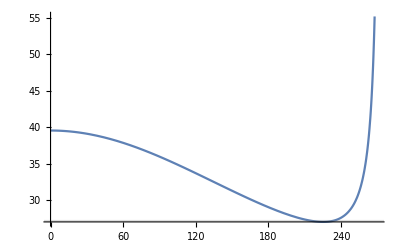

```mathematica
Plot[{σzz09/.dext->dext0},{dint,0,270},GridLines->{None,{σzz09/.dext->dext0/.dint->dint0}}]
```

As-it-is stress state in [MPa]:

```mathematica
σzz00/.dint->dint0/.dext->dext0
```

59.0624

```mathematica
σzz09/.dint->dint0/.dext->dext0
```

27.2512

Given the yielding stress  in [MPa], the as-it-is STATIC safety factor is:

```mathematica
σY = 200;
ϕ00 = σY/(σzz00/.dint->dint0/.dext->dext0)
```

3.38625

```mathematica
ϕ09 = σY/(σzz09/.dint->dint0/.dext->dext0)
```

7.33913

### AS-IT-IS INSTABILITY ANALYSIS (Carico di punta)

As stated before, while pushing the bar works in compression; this leads to an instability problem that can be analyzed with the Euler formulas.
The aim is to evaluate the maximum permissible axial load on the middle bar and verify the as-it-is dimensions.

```mathematica
(*Young's elastic modulus [MPa]*)
EY = 210000;
```

The first Euler critical load is:

```mathematica
Pcr1 = N[π^2*EY*Ix/Lbar^2](*[MPa*mm^4/mm^2]=[N], where Lbar0 is the minimum length needed to avoid instability*)
```

0.00149479 (dext^4-1. dint^4)

The as-it-is critical load is:

```mathematica
Pcr10 =N@ Pcr1/.dint->dint0/.dext->dext0(*[N]*)
```

5.22613×10^6

We state then the maximum admissible stress as:

```mathematica
σcr = FullSimplify@(Pcr1/A)(*[N/mm^2]=[MPa]*)
```

0.00190323 dext^2+0.00190323 dint^2

```mathematica
σcr0=σcr/.dint->dint0/.dext->dext0
```

228.193

Note that this stress  is greater than the yielding one, so it’s not the critical failure.

### DIAMETERS OPTIMIZATIONS

The aim is to find the smallest possible cross section which produces a reasonable safety factor in order to reduce material consumption.
The approach is to set dext = dext0 = 273 (which is needed in order to fix the revolute joints) and vary dint.

dint will be evaluated for 2 different critical stresses for each load configuration (single actuator or double actuator), the static and the instability stresses.
For STATIC verification we use a safety factor ϕs .
For INSTABILITY verification we use a safety factor ϵi .

```mathematica
ϕs = 4;
ϵi = 3;
```

```mathematica
(*STATIC 00*)
NSolve[ϕs*σzz00==σY/.dext->dext0,dint]
```

{{dint→168.93},{dint→-168.93},{dint→-87.8649},{dint→87.8649}}

```mathematica
(*STATIC 09*)
NSolve[ϕs*σzz09==σY/.dext->dext0,dint]
```

{{dint→-266.735},{dint→266.735},{dint→0.-127.818 ⅈ},{dint→0.+127.818 ⅈ}}

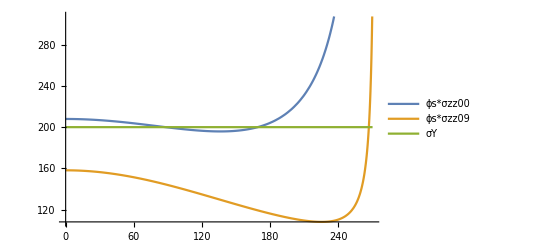

```mathematica
Plot[{
ϕs*σzz00/.dext->dext0,
ϕs*σzz09/.dext->dext0,
σY
},{dint,0,270},PlotLegends->{"ϕs*σzz00","ϕs*σzz09","σY"}]
```

For STATIC dimensioning, there are 2 real positive solutions in 00 condition, and a single real positive one for 09 condition.

```mathematica
(*INSTABILITY 00*)
NSolve[ϵi*σzz00==σcr/.dext->dext0,dint]
```

{{dint→0.-371.162 ⅈ},{dint→0.+371.162 ⅈ},{dint→241.016},{dint→-241.016},{dint→71.7198},{dint→-71.7198}}

```mathematica
(*INSTABILITY 09*)
NSolve[ϵi*σzz09==σcr/.dext->dext0,dint]
```

{{dint→0.-375.637 ⅈ},{dint→0.+375.637 ⅈ},{dint→270.452},{dint→-270.452},{dint→0.-81.0581 ⅈ},{dint→0.+81.0581 ⅈ}}

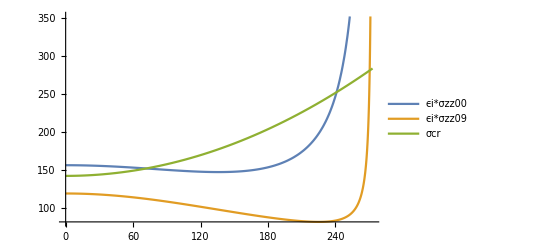

```mathematica
Plot[{
ϵi*σzz00/.dext->dext0,
ϵi*σzz09/.dext->dext0,
σcr/.dext->dext0
},{dint,0,273},PlotLegends->{"ϵi*σzz00","ϵi*σzz09","σcr"}]
```

For INSTABILITY dimensioning, there are 2 real positive solutions in 00 condition, and a single real positive one for 09 condition.

The strange result is that the solution exhibit more than one real positive solution; this is because varying the internal diameter, the contribution of the beam weight changes as well and it’s not negligible.

Selecting an internal diameter of 170:

```mathematica
σzz00/.dext->dext0/.dint->170(*[MPa]*)
```

50.0813

```mathematica
σzz00/.dext->dext0/.dint->dint0(*[MPa]*)
```

59.0624

```mathematica
σzz09/.dext->dext0/.dint->170
```

29.7518

```mathematica
σzz09/.dext->dext0/.dint->dint0
```

27.2512

```mathematica
W/.dext->dext0/.dint->170(*bar weight[kg]*)
```

22622.9

```mathematica
W0
```

14457.6